# Development

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["AnalyticalSolarDevices`","C:\\Users\\Liu Haohui\\OneDrive - envision\\Development\\Analytical models development\\analytical-solar-cell-and-module\\AnalyticalSolarDevices.wl"];
Needs["AnalyticalPVStrings`","C:\\Users\\Liu Haohui\\OneDrive - envision\\Development\\Analytical models development\\Analytical-PV-string\\AnalyticalPVStrings.wl"];
T=298.15;
spec=<<spectrum_AM15G;

Off[InterpolatingFunction::dmval];
```

## IV curve combine

## generate IV for different irradiance levels

```mathematica
irrLvs=Append[RandomVariate[NormalDistribution[1,0.1],10],0.5];
```

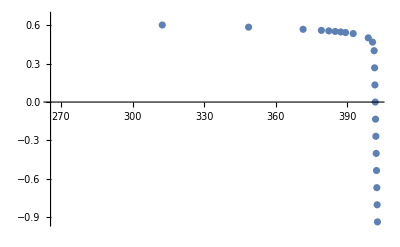

```mathematica
IV$singleCell=Interpolation[Reverse/@First@SiCell[spec,T,DeviceParameters->parameters["PERC"],CellQE->EQE["PERC"]]];
IV$singleCell//ListPlot
```

```mathematica
IV$fleet=(DeleteDuplicatesBy[Round[Reverse/@First@SiCell[#,T,DeviceParameters->parameters["PERC"],CellQE->EQE["PERC"]],0.00001]
,First]&)/@Table[Transpose[specᵀ*{1,i}],{i,irrLvs}];
```

```mathematica
Min[IV$fleet⟦All,-1,1⟧]
```

201.741

```mathematica
IV$fleet[[-1]]
```

{{0.,0.65183},{84.5471,0.6301},{139.89,0.60837},{171.298,0.58665},{184.184,0.57035},{188.381,0.5622},{190.065,0.55813},{191.519,0.55405},{192.772,0.54998},{193.851,0.54591},{195.576,0.53776},{197.785,0.52146},{199.624,0.48887},{200.17,0.45628},{200.421,0.3911},{200.568,0.26073},{200.698,0.13037},{200.828,0.},{200.959,-0.13037},{201.089,-0.26073},{201.22,-0.3911},{201.35,-0.52146},{201.48,-0.65183},{201.611,-0.78219},{201.741,-0.91256}}

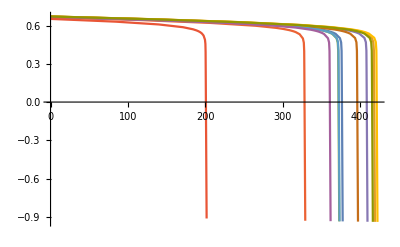

```mathematica
IV$fleet//ListLinePlot
```

## Combine without bypass diodes

```mathematica
combinedIV=With[{range=Range[0,Min@IV$fleet⟦All,-1,1⟧]},{range,Total@Table[Interpolation[IV$fleet⟦i⟧,InterpolationOrder->1][x],{i,Length@IV$fleet},{x,range}]}ᵀ];
```

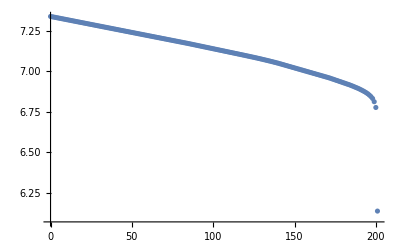

```mathematica
combinedIV//ListPlot[#,PlotRange->All]&
```

```mathematica
probe=combinedIV⟦-1,1⟧*1.01;
```

```mathematica
{probe,Total@Table[Interpolation[IV$fleet⟦i⟧,InterpolationOrder->1][probe],{i,Length@IV$fleet}]}
```

InterpolatingFunction::dmval: Input value {203.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

{203.01,4.1214}

```mathematica
While[combinedIV⟦-1,2⟧>-0.4,
probe=combinedIV⟦-1,1⟧*1.01;
AppendTo[combinedIV,{probe,Total@Table[Interpolation[IV$fleet⟦i⟧,InterpolationOrder->1][probe],{i,Length@IV$fleet}]}];]
```

InterpolatingFunction::dmval: Input value {203.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {205.04} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {207.091} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

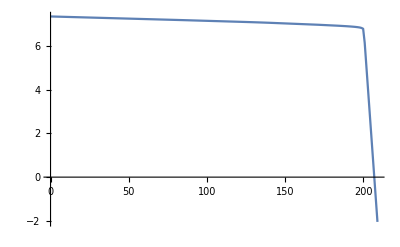

```mathematica
combinedIV//ListLinePlot[#,PlotRange->All]&
```

## Combine with bypass diode

```mathematica
Interpolation[IV$fleet⟦-1⟧,InterpolationOrder->1][10000]
```

InterpolatingFunction::dmval: Input value {10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

-9800.67

### Side track: optimize computation time

```mathematica
AbsoluteTiming[With[{range=Range[0,Max@IV$fleet⟦All,-1,1⟧]},
{range,Total@Table[
If[Interpolation[IV$fleet⟦i⟧,InterpolationOrder->1][x]<-0.5,-0.5,Interpolation[IV$fleet⟦i⟧,InterpolationOrder->1][x]]
,{i,Length@IV$fleet},{x,range}]}ᵀ];]
```

InterpolatingFunction::dmval: Input value {378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {379} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {380} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.334179,Null}

```mathematica
AbsoluteTiming[With[{range=Range[0,Max@IV$fleet⟦All,-1,1⟧]},
{range,Total@Table[
With[{interp=Interpolation[IV$fleet⟦i⟧,InterpolationOrder->1]},
	If[interp[x]<-0.5,-0.5,interp[x]]]
,{i,Length@IV$fleet},{x,range}]}ᵀ];]
```

InterpolatingFunction::dmval: Input value {378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {379} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {380} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.203718,Null}

```mathematica
AbsoluteTiming[With[{range=Range[0,Max@IV$fleet⟦All,-1,1⟧]},
{range,Total@Table[
With[{interp=Interpolation[IV$fleet⟦i⟧,InterpolationOrder->1]},
	Table[If[interp[x]<-0.5,-0.5,interp[x]],{x,range}]
]
,{i,Length@IV$fleet}]}ᵀ];]
```

{0.0194121,Null}

```mathematica
AbsoluteTiming[With[{range=Range[0,Max@IV$fleet⟦All,-1,1⟧]},
{range,Total@Table[
With[{interp=Interpolation[IV$fleet⟦i⟧,InterpolationOrder->1]},
	Table[With[{interpPt=interp[x]},If[interpPt<-0.5,-0.5,interpPt]],{x,range}]
]
,{i,Length@IV$fleet}]}ᵀ];]
```

{0.0146263,Null}

### Continue:

```mathematica
combinedIV=With[{range=Range[0,Max@IV$fleet⟦All,-1,1⟧]},
{range,Total@Table[
With[{interp=Interpolation[IV$fleet⟦i⟧,InterpolationOrder->1]},
	Table[With[{interpPt=interp[x]},If[interpPt<-0.5,-0.5,interpPt]],{x,range}]
]
,{i,Length@IV$fleet}]}ᵀ];
```

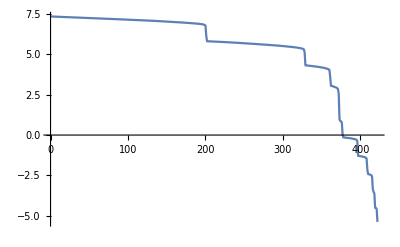

```mathematica
combinedIV//ListLinePlot[#,PlotRange->All]&
```

```mathematica
IV$fleetInterp=Interpolation[#,InterpolationOrder->1]&/@IV$fleet;
Jmin=combinedIV⟦-1,1⟧;
probe=Jmin*1.01;
While[combinedIV⟦-1,2⟧>-0.6*Length@IV$fleet&&probe<Jmin*1.05,
probe=combinedIV⟦-1,1⟧*1.01;
AppendTo[combinedIV,{probe,Total@Table[
With[{interpPt=IV$fleetInterp⟦i⟧[probe]},If[interpPt<-0.5,-0.5,interpPt]]
,{i,Length@IV$fleet}]}];]
```

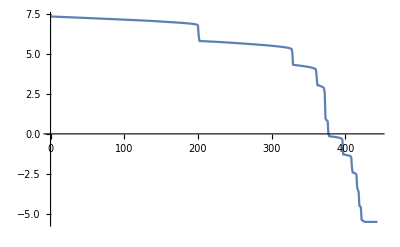

```mathematica
combinedIV//ListLinePlot[#,PlotRange->All]&
```

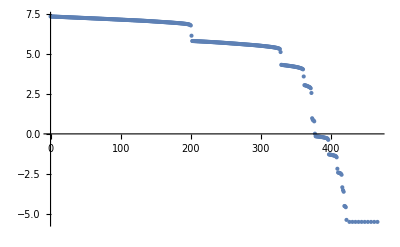

```mathematica
StringIV[IV$fleet,"BypassDiode"->True]//ListPlot[#,PlotRange->All]&
```

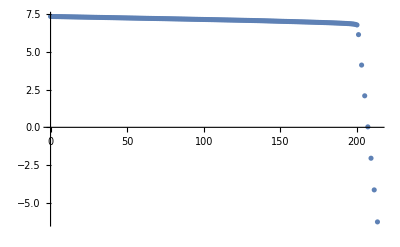

```mathematica
StringIV[IV$fleet,"BypassDiode"->False]//ListPlot[#,PlotRange->All]&
```

## MPPT

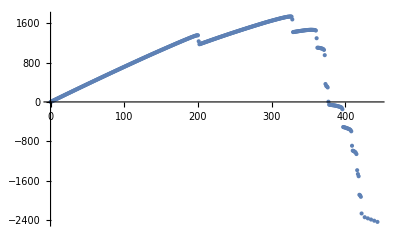

```mathematica
{First@#,Times@@#}&/@combinedIV//ListPlot
```

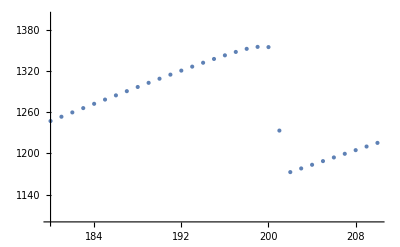

```mathematica
{First@#,Times@@#}&/@combinedIV//ListPlot[#,PlotRange->{{180,210},{1100,1400}}]&
```

```mathematica
IVP=Append[#,Times@@#]&/@combinedIV;
```

```mathematica
MaximalBy[IVP,Last,1]//AbsoluteTiming
```

{0.000254,{{326,5.33164,1738.11}}}

```mathematica
IVP~Extract~Position[#,Max@#]&@Part[IVPᵀ,3]//AbsoluteTiming
```

{0.0001369,{{326,5.33164,1738.11}}}

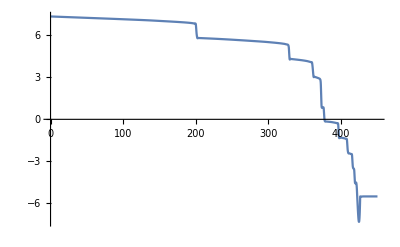

```mathematica
Plot[Interpolation[combinedIV,InterpolationOrder->3][x],{x,0,450}]
```

```mathematica
FindMaximum[Interpolation[combinedIV,InterpolationOrder->3][x]*x,{x,350},AccuracyGoal->6,PrecisionGoal->6]//AbsoluteTiming
```

{0.0014778,{1467.17,{x→353.56}}}

```mathematica
NMaximize[Interpolation[combinedIV,InterpolationOrder->3][x]*x,x,AccuracyGoal->6,PrecisionGoal->6]//AbsoluteTiming
```

{0.170653,{1738.14,{x→325.892}}}

```mathematica
NMaximize[{Interpolation[combinedIV,InterpolationOrder->3][x]*x,{0≤x<550}},x,AccuracyGoal->5,PrecisionGoal->5]//AbsoluteTiming
```

{0.0479079,{1739.72,{x→326.418}}}

```mathematica
{x/.#[[2,1]],Interpolation[combinedIV,InterpolationOrder->3][x/.#[[2,1]]],First@#}&@{1739.7213500605828,{x->326.4184665690626}}
```

{326.418,5.32973,1739.72}

```mathematica
MPPT[combinedIV]
```

{326,5.33164,1738.11}

```mathematica
MPPT[combinedIV,TrackingMethod->"Robust"]
```

{326.418,5.32973,1739.72}

## c-Si Module IV

```mathematica
metalFraction=0.03;
cellArea=.024432; (*area to receive light*)
Rs=0.006; (* per solar cell, in Ohm *)
Rsh=8;
parameters["userPERCcell"]=<|"J01"->2*10^-9,"J02"->1*10^-6,"Rs"->Rs*cellArea,"Rsh"->Rsh*cellArea|>;
```

```mathematica
cell1=SiCell[spec,T,DeviceParameters->parameters["PERC"],DeviceQE->EQE["PERC"],DeviceArea->cellArea,MetalCoverage->metalFraction]
```

{{{0.668922,-4.48652×10^-12},{0.646624,3.19294},{0.624327,5.70338},{0.602029,7.45196},{0.602029,7.45196},{0.585306,8.29553},{0.568583,8.82409},{0.564403,8.91842},{0.560222,9.00059},{0.556041,9.07195},{0.55186,9.13376},{0.543499,9.23321},{0.535137,9.30689},{0.501691,9.45126},{0.468245,9.49226},{0.401353,9.50795},{0.267569,9.51234},{0.133784,9.51562},{0.,9.51888},{-0.133784,9.52215},{-0.267569,9.52542},{-0.401353,9.52869},{-0.535137,9.53196},{-0.668922,9.53523},{-0.802706,9.53849},{-0.93649,9.54176}},9.51974,0.668922,0.79215,5.04438,9.07195,0.556041}

```mathematica
cell1[[5]]/cellArea
```

206.466

```mathematica
cell2=SiCell[spec,T,DeviceParameters->parameters["userPERCcell"],DeviceQE->EQE["PERC"],DeviceArea->cellArea,MetalCoverage->metalFraction]
```

{{{0.66871,-1.15706×10^-14},{0.64642,2.43481},{0.624129,4.58047},{0.601839,6.35126},{0.568403,8.15767},{0.551686,8.68479},{0.543327,8.87156},{0.539147,8.94896},{0.534968,9.01697},{0.530788,9.07653},{0.526609,9.12851},{0.51825,9.21302},{0.501532,9.32377},{0.468097,9.41864},{0.401226,9.4597},{0.267484,9.47917},{0.133742,9.4959},{0.,9.51261},{-0.133742,9.52931},{-0.267484,9.54602},{-0.401226,9.56272},{-0.534968,9.57943},{-0.66871,9.59613},{-0.802452,9.61284},{-0.936194,9.62954}},9.51974,0.66871,0.757909,4.82481,8.94896,0.539147}

```mathematica
cell2[[5]]/cellArea
```

197.479

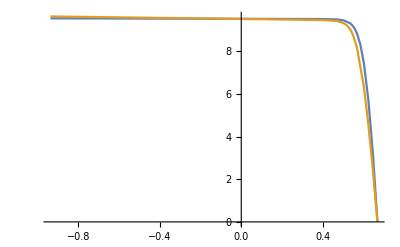

```mathematica
ListLinePlot[First/@{cell1,cell2}]
```

```mathematica
iv=DeleteDuplicatesBy[Round[Reverse/@First@cell1,0.00001]
,First]
```

{{0.,0.66892},{3.19294,0.64662},{5.70338,0.62433},{7.45196,0.60203},{8.29553,0.58531},{8.82409,0.56858},{8.91842,0.5644},{9.00059,0.56022},{9.07195,0.55604},{9.13376,0.55186},{9.23321,0.5435},{9.30689,0.53514},{9.45126,0.50169},{9.49226,0.46825},{9.50795,0.40135},{9.51234,0.26757},{9.51562,0.13378},{9.51888,0.},{9.52215,-0.13378},{9.52542,-0.26757},{9.52869,-0.40135},{9.53196,-0.53514},{9.53523,-0.66892},{9.53849,-0.80271},{9.54176,-0.93649}}

```mathematica
moduleIV=StringIV[{Reverse/@cell2[[1]],Reverse/@cell2[[1]]}]
```

{{0,1.33742},{1,1.31911},{2,1.3008},{3,1.2811},{4,1.26032},{5,1.2377},{6,1.21252},{7,1.17966},{8,1.14264},{9,1.07203},{9.09,1.05941},{9.1809,1.04285},{9.27271,1.01848},{9.36544,0.973698},{9.45909,0.804422},{9.55368,-0.657699},{9.64922,-1.},{9.74571,-1.},{9.84317,-1.},{9.9416,-1.}}

```mathematica
moduleIV=StringIV[ConstantArray[Reverse/@First@cell2,60]]
```

{{0,40.1226},{1,39.5733},{2,39.024},{3,38.4329},{4,37.8096},{5,37.1309},{6,36.3757},{7,35.3898},{8,34.2791},{9,32.1608},{9.09,31.7823},{9.1809,31.2856},{9.27271,30.5544},{9.36544,29.2109},{9.45909,24.1327},{9.55368,-19.731},{9.64922,-30.},{9.74571,-30.},{9.84317,-30.},{9.9416,-30.}}

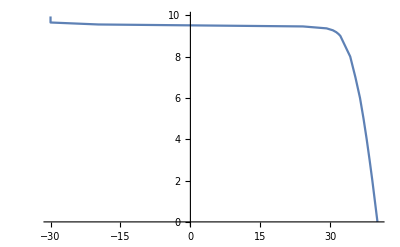

```mathematica
Reverse/@moduleIV//ListLinePlot
```

## Generate IV set: various scenarios

## Partial shading